```mathematica
(*this notebook draws the bifurcation diagrams. Run with empty kernel (restart Mathematica)*)
(*directory for exporting plots*)
outputdirectory=NotebookDirectory[];
(*name of model*)
model="mech-simple";
(*state variables*)
vars[model]={c,p,b1,b2};
(*function to find equilibria*)
equilibrium[model][{
ac1_,ac2_,hc_,mc_,
ap1_,ap2_,hp_,mp_,
w1_,w2_,
δ_,
k_,yc_,yp_,l_
},constraints_]:=Module[{g,f,h,uc,ucs,lc,up,ups,lp,ub1,uc1,up1,ub2,uc2,up2},
(*functions for model*)
f[a_,h_][x_]:=(a  x)/(1+a h x);
h[a1_,a2_,h_][x1_,x2_][y1_,y2_]:=(a1 y1+a2 y2)/(1+a1 h x1+a2 h x2);
ub1=w1;
ub2=w2;
uc1=h[ac1,ac2,hc][b1,b2][b1,0] c;
uc2=h[ac1,ac2,hc][b1,b2][0,b2] c;
uc=uc1+uc2;
lc=mc c;
up1=h[ap1,ap2,hp][b1,b2][b1,0] p;
up2=h[ap1,ap2,hp][b1,b2][0,b2] p;
up=up1+up2;
lp=(1-l/(l+k))mp p;
(*right hand side of differential equations*)
eqs={
ub1-uc1-up1-δ b1,
ub2-uc2-up2-δ b2,
yc uc-lc,
yp up-lp
};
(*solve right hand sides for equilibrium*) 
NSolve[Join[{eqs==0},constraints],vars[model]]
];
(*parameter values*)
testparspre[model]={ac1->0.0001174306138293696,ac2->0.0005176312987229842,hc->5.160474332874365*^-8,mc->0.3496210885916874,ap1->0.0009562096982402928,ap2->0.00010652428211175634,hp->3.0190588360555664*^-7,mp->0.43682757303900366,w1->8.909849219878205*^8,w2->4.750937855377403*^8,δ->0.02156116874263299,k->62.09292855815097,yc->1/10000000,yp->1/10000000,l->50};
pars[model]=testparspre[model][[All,1]];
(*find equilibria for range of light levels*)
list[model]=Table[{ll,equilibrium[model][pars[model]/.l->ll/.testparspre[model],{b1≥0,b2≥0,c≥0,p≥0}]},{ll,0,200,1}];
```

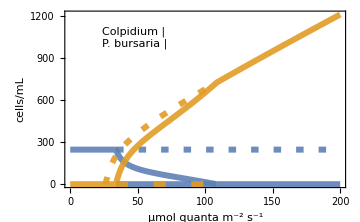

```mathematica
(*function to bring bifurcation list in right shape*)
extract[list_,var_]:=Flatten[Table[Table[{l[[1]],var/.x},{x,l[[2]]}],{l,list}],1];
(*find for which light levels there are 4 or more equilibria (to connect the right branches of the equilibria)*)
{t2,t3}=Select[list[model],Length@#[[2]]≥4&][[{1,-1},1]];
(*first time when there are 3 or more equilibria*)
t1=Select[list[model],Length@#[[2]]≥3&][[1,1]];
(*conditions for choosing equilibria branches*)
conditions={#[[1]]<t1&,t1≤#[[1]]<t2&,t2≤#[[1]]≤t3&,t3<#[[1]]&};
(*seperate list of equilbria to multiple lists according to conditions*)
lists=Table[Select[list[model],cond],{cond,conditions}];
(*lists for Colpidium*)
listc1=Join[
{#[[1]],Max[c/.#[[2]]]}&/@lists[[1]],{#[[1]],Max[c/.#[[2]]]}&/@lists[[2]],{#[[1]],Sort[c/.#[[2]]][[3]]}&/@lists[[3]],
{#[[1]],Min[c/.#[[2]]]}&/@lists[[4]]
];
listc2=Join[
{#[[1]],Max[c/.#[[2]]]}&/@lists[[3]],{#[[1]],Max[c/.#[[2]]]}&/@lists[[4]]
];
listc3=Join[
{#[[1]],Min[c/.#[[2]]]}&/@lists[[1]],{#[[1]],Min[c/.#[[2]]]}&/@lists[[2]],{#[[1]],Min[c/.#[[2]]]}&/@lists[[3]]
];
(*lists for Paramecium*)
listp1=Join[
{#[[1]],Min[p/.#[[2]]]}&/@lists[[1]],
{#[[1]],Min[p/.#[[2]]]}&/@lists[[2]],{#[[1]],Sort[p/.#[[2]]][[3]]}&/@lists[[3]],{#[[1]],Max[p/.#[[2]]]}&/@lists[[4]]
];
listp2=Join[
{#[[1]],Min[p/.#[[2]]]}&/@lists[[3]],{#[[1]],Min[p/.#[[2]]]}&/@lists[[4]]
];
listp3=Join[
{{#[[1]],Min[p/.#[[2]]]}&@lists[[1,-1]]},
{#[[1]],Sort[p/.#[[2]]][[3]]}&/@lists[[2]],
{#[[1]],Sort[p/.#[[2]]][[4]]}&/@lists[[3]]
];
(*style for plot*)
cols=ColorData[97]/@{1,2};
legendstyle=11;
legendbifurcation=Framed[Grid[Table[{Style[{"Colpidium","P. bursaria"}[[i]],legendstyle,Italic],Plot[.5,{x,0,1},PlotStyle->{{Thickness[.14],cols[[i]]}},Axes->None,ImageSize->20,PlotRange->{0,1}]},{i,{1,2}}],Alignment->{Center,Center}],RoundingRadius->5];
dashing1=Dashing[{.015,.03}];
dashing2=Dashing[.8{ .03,.064}];
thickness=Thickness[.012];
lightplotstyle={ImagePadding->{{65,45},{38,10}},LabelStyle->11,ImageSize->Medium,BaseStyle->{Opacity->0.9}};
(*plot bifurcation*)
plotA=ListPlot[{listc1,listc2,listp1,listp3,{{t2,0},{t3,0}},{{t2,0},{t3,0}}},Joined->True,PlotStyle->{{cols[[1]],thickness},{dashing1,cols[[1]],thickness},{cols[[2]],thickness},{dashing1,cols[[2]],thickness},{cols[[1]],thickness},{cols[[2]],dashing2,thickness}},Frame->{True,True,False,False},lightplotstyle,FrameLabel->{{"cells/mL",Null},{"μmol quanta m^-2 s^-1",Null}},PlotRange->Full,Epilog->Inset[legendbifurcation,Scaled[{.25,.85}]],PlotRangeClipping->{{True,True},{False,False}},ImagePadding->{{Automatic,105},{Automatic,Automatic}}
,LabelStyle->11]
```

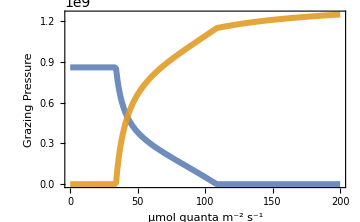
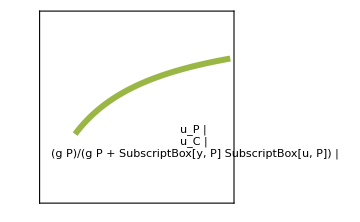

```mathematica
(*define functions for plotting derived quantities*)
h[a1_,a2_,h_][x1_,x2_][y1_,y2_]:=(a1 y1+a2 y2)/(1+a1 h x1+a2 h x2);
ub1=w1;
ub2=w2;
uc1=h[ac1,ac2,hc][b1,b2][b1,0] c;
uc2=h[ac1,ac2,hc][b1,b2][0,b2] c;
uc=uc1+uc2;
lc=mc c;
up1=h[ap1,ap2,hp][b1,b2][b1,0] p;
up2=h[ap1,ap2,hp][b1,b2][0,b2] p;
up=up1+up2;
lp=(1-l/(l+k))mp p;
addlight[list_]:=Table[{x[[1]],Join[{l->x[[1]]},#]&/@x[[2]]},{x,list}];
ps=l/(l+k)mp;
pbact=p (h[ap1,ap2,hp][b1,b2][b1,0]+h[ap1,ap2,hp][b1,b2][0,b2]);
cbact=c (h[ac1,ac2,hc][b1,b2][b1,0] +h[ac1,ac2,hc][b1,b2][0,b2]);
plotf=Piecewise[{{(ps p)/(yp pbact+ps p), p>0}, {0, True}}];
(*apply function to list (choosing equilbrium with pos)*)
getlist[f_,list_,pos_]:={#[[1]],f/.Sort[#[[2]],(p/.#1)≤(p/.#2)&][[pos]]/.testparspre[model]}&/@addlight[list];
(*apply functions to plot to lists*)
listgs=Table[Join[
getlist[f,lists[[1]],1],
getlist[f,lists[[2]],1],
getlist[f,lists[[3]],-2],
getlist[f,lists[[4]],-1]
],{f,{plotf,pbact,cbact}}];
(*style for plots, legends*)
colPS=ColorData[97][3];
legendplot2=Framed[Grid[Table[{Style[{"u_P","u_C","(g P)/(g P + SubscriptBox[y, P] SubscriptBox[u, P])"}[[i]],legendstyle,Italic],Plot[.5,{x,0,1},PlotStyle->{{Thickness[.14],Join[cols,{colPS}][[i]](*,{None,None,Dashing[.3]}[[i]]*)}},Axes->None,ImageSize->20,PlotRange->{0,1}]},{i,3}],Alignment->{Center,Center}],RoundingRadius->5,Background->White];
lightplotstyle={ImagePadding->{{65,45},{38,10}},LabelStyle->11,ImageSize->Medium,BaseStyle->{Opacity->0.9}};
(*plot up and uc*)
plot1=ListPlot[listgs[[{3,2}]],PlotStyle->({thickness,#}&/@cols),
Frame->{True,True,False,False},FrameStyle->{Automatic,Automatic,Automatic,Automatic},FrameLabel->{{"Grazing Pressure",Null},{"μmol quanta m^-2 s^-1",Null}},PlotRange->{0,Full},Evaluate@lightplotstyle,
PlotRange->{{0,200},Full},Joined->True];
(*plot proportion of photosynthesis*)
plot2=ListPlot[Select[listgs[[1]],#[[2]]>0&],PlotStyle->{thickness,colPS},
Frame->{False,False,False,True},FrameLabel->{{Null,"Prop. Phot. Growth"},{Null,Null}},
PlotRange->{{0,200},{0,1}},Evaluate@lightplotstyle,FrameStyle->{Automatic,Automatic,Automatic,colPS},Epilog->Inset[legendplot2,Scaled[{.8,.32}]],FrameTicks->{{None,All},{None,None}},Joined->True
];
(*show plots together*)
plotB=Overlay[{plot1,plot2}]
```

```mathematica
(*stack the bifurcations and export*)
(Export[outputdirectory<>"bifurcations.pdf",#];#)&@Column[{plotA,plotB}]
```

-Graphics-
-Graphics--Graphics-